# Laboratorio 2, Mat1620L

## Preguntas

### 1)

#### Solución

a) Notemos que P_n(1) es una serie alternante. Entonces podemos ocupar el siguiente teorema:

-Graphics-

```mathematica
b[n_]:=1/(2 n)!
Reduce[{b[n+1]<10^-3,n>0},n,Integers]
```

(2 (1+n))!∈ℝ&&n∈ℤ&&n≥3

Vemos que con n≥3 cumple lo pedido.  Lo comprobamos con el siguiente código:

```mathematica
p3[x_]:=Sum[(-1)^k x^(2 k)/(2 k)!,{k,0,3}]
Abs[Cos[1]-p3[1]]<10^-3
```

True

b) Podemos definir los polinomios con la siguiente sintaxis:

```mathematica
ClearAll["Global`*"]
f[x_]:=Cos[x]
p[n_,x_]:=Sum[(-1)^k x^(2 k)/(2 k)!,{k,0,n}]
p[1,x]
p[2,x]
p[3,x]
p[4,x]
p[5,x]
p[6,x]
```

1-x^2/2

1-x^2/2+x^4/24

1-x^2/2+x^4/24-x^6/720

1-x^2/2+x^4/24-x^6/720+x^8/40320

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+x^12/479001600

c)

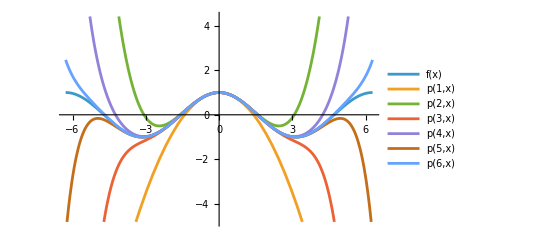

```mathematica
Plot[{f[x],p[1,x],p[2,x],p[3,x],p[4,x],p[5,x],p[6,x]},{x,-2Pi,2Pi},PlotLegends->"Expressions"]
```

d)

```mathematica
Manipulate[Plot[{f[x],p[n,x]},{x,-4 Pi,4 Pi},PlotRange->{{-4 Pi,4 Pi},{-1,1}},PlotLegends->{"Cos[x]","p_n[x]"}],{n,0,20,1}]
```

### 2)

#### Solución

a)

```mathematica
Reduce[{4/(2 n+1)<10^-3,n>=1},n,Integers]
```

n∈ℤ&&n≥2000

La cota del resto permite garantizar la precisión con 2000 términos. Sin embargo, al calcular directamente el error se observa que 1000 términos ya producen un error menor que 10^{-3}. Esto no contradice la estimación anterior, ya que la cota del resto es una cota superior y no necesariamente coincide con el error real.

```mathematica
p[n_,x_]:=Sum[(-1)^(k+1) x^(2 k-1)/(2 k-1),{k,1,n}]
N[Abs[4 p[1000,1]-Pi],15]
```

0.000999999750000312

b) Notemos que no necesitamos realizar el calculo. Solo debemos encontrar el n que asegura lo pedido.

```mathematica
Reduce[{4/(2 n+1)<10^-10,n>=1},n,Integers]
```

n∈ℤ&&n≥20000000000

c) Necesitamos que p_n(x) converja para x=1/2 y x=1/3 al mismo tiempo. Notemos que si ambas series convergen, entonces

ArcTan(1/2)+ArcTan(1/3)=∑_(k=1)^∞ (-1)^(k+1)/(2^(2k-1)(2k-1))+∑_(k=1)^∞ (-1)^(k+1)/(3^(2k-1)(2k-1))=∑_(k=1)^∞ (-1)^(k+1)(1/(2^(2k-1)(2k-1))+1/(3^(2k-1)(2k-1)))

```mathematica
Reduce[{4 (1/(2^(2 n+1) (2 n+1))+1/(3^(2 n+1) (2 n+1)))<10^-3,n>=1},n,Integers]
```

n∈ℤ&&n≥4

d) Necesitamos que p_n(x) converja para x=1/5 y x=1/239 al mismo tiempo. Notemos que si ambas series convergen, entonces

4ArcTan(1/5)-ArcTan(1/239)=4∑_(k=1)^∞ (-1)^(k+1)/(5^(2k-1)(2k-1))-∑_(k=1)^∞ (-1)^(k+1)/(239^(2k-1)(2k-1))=∑_(k=1)^∞ (-1)^(k+1)(4/(5^(2k-1)(2k-1))-1/(239^(2k-1)(2k-1)))

Notemos que 4/(5^(2k-1)(2k-1))-1/(239^(2k-1)(2k-1)) es siempre positivo.

```mathematica
Reduce[{16/(5^(2 n+1) (2 n+1))+4/(239^(2 n+1) (2 n+1))<10^-3,n>=1},n,Integers]
```

n∈ℤ&&n≥3

De lo anterior vemos que como necesitamos que ambas series converjan, entonces con n≥4 ya podemos asegurar la precisión pedida. Podemos comprobar, “a mano”, que con solo 2 términos ya tenemos la precisión pedida.

```mathematica
N[Abs[16 Sum[(-1)^(k+1) (1/5)^(2 k-1)/(2 k-1),{k,1,2}]-4 Sum[(-1)^(k+1) (1/239)^(2 k-1)/(2 k-1),{k,1,2}]-Pi],15]
N[Abs[16 Sum[(-1)^(k+1) (1/5)^(2 k-1)/(2 k-1),{k,1,3}]-4 Sum[(-1)^(k+1) (1/239)^(2 k-1)/(2 k-1),{k,1,3}]-Pi],15]
```

0.000995624263732924

0.0000283757352411866

e) De todo lo anterior podemos ver que el método descrito en d) es el mas efectivo.